```mathematica
a={3,3,-4,1};
```

```mathematica
b={5,3,-4,1};
```

```mathematica
d={3,5,-4,1};
```

```mathematica
c={5,5,-4,1};
```

```mathematica
aPrime={3,3,-6,1};
```

```mathematica
bPrime={5,3,-6,1};
```

```mathematica
cPrime={5,5,-6,1};
```

```mathematica
dPrime={3,5,-6,1};
e= {17,18,-19,1};
```

```mathematica
Oc={0,0,0,1};
Oc2={6,0,0,1};
t:=1/Sqrt[2];
```

```mathematica
M={{t,0,-t,-6t},{0,1,0,0},{t,0,t,-6t},{0,0,0,1}};
```

```mathematica
a
```

1/(√2)

```mathematica
M
```

{{1/(√2),0,-1/(√2),-3 √2},{0,1,0,0},{1/(√2),0,1/(√2),-3 √2},{0,0,0,1}}

```mathematica
PM={{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};
```

```mathematica
ProjektionsMatrixKamera2=PM.M;
```

```mathematica
MatrixForm[ProjektionsMatrixKamera2];
```

```mathematica
MatrixForm[{{-1/(√2),0,1/(√2),3 √2},{0,-1,0,0},{-1/(√2),0,-1/(√2),3 √2},{1/(√2),0,1/(√2),-3 √2}}]
```

(-1/(√2) | 0 | 1/(√2) | 3 √2
0 | -1 | 0 | 0
-1/(√2) | 0 | -1/(√2) | 3 √2
1/(√2) | 0 | 1/(√2) | -3 √2)

```mathematica
aK2=ProjektionsMatrixKamera2.a;
```

```mathematica
{-3/(√2)+√2,-3,-3/(√2)+5 √2,3/(√2)-5 √2}
```

{-3/(√2)+√2,-3,-3/(√2)+5 √2,3/(√2)-5 √2}

```mathematica
bK2=ProjektionsMatrixKamera2.b;
```

```mathematica
{-5/(√2)+√2,-3,-5/(√2)+5 √2,5/(√2)-5 √2}
```

{-5/(√2)+√2,-3,-5/(√2)+5 √2,5/(√2)-5 √2}

```mathematica
cK2=ProjektionsMatrixKamera2.c;
```

```mathematica
{-5/(√2)+√2,-5,-5/(√2)+5 √2,5/(√2)-5 √2}
```

{-5/(√2)+√2,-5,-5/(√2)+5 √2,5/(√2)-5 √2}

```mathematica
dK2=ProjektionsMatrixKamera2.d;
```

```mathematica
{-3/(√2)+√2,-5,-3/(√2)+5 √2,3/(√2)-5 √2}
```

{-3/(√2)+√2,-5,-3/(√2)+5 √2,3/(√2)-5 √2}

```mathematica
eK2=ProjektionsMatrixKamera2.e;
```

```mathematica
{-15 √2,-18,4 √2,-4 √2}
```

{-15 √2,-18,4 √2,-4 √2}

```mathematica
dPrimeK2=ProjektionsMatrixKamera2.dPrime;
```

```mathematica
{-3/(√2),-5,-3/(√2)+6 √2,3/(√2)-6 √2}
```

{-3/(√2),-5,-3/(√2)+6 √2,3/(√2)-6 √2}

```mathematica
aPrimeK2=ProjektionsMatrixKamera2.aPrime;
```

```mathematica
{-3/(√2),-3,-3/(√2)+6 √2,3/(√2)-6 √2}
```

{-3/(√2),-3,-3/(√2)+6 √2,3/(√2)-6 √2}

```mathematica
bPrimeK2 = ProjektionsMatrixKamera2.bPrime;
```

```mathematica
{-5/(√2),-3,-5/(√2)+6 √2,5/(√2)-6 √2}
```

{-5/(√2),-3,-5/(√2)+6 √2,5/(√2)-6 √2}

```mathematica
cPrimeK2=ProjektionsMatrixKamera2.cPrime;
```

```mathematica
{-5/(√2),-5,-5/(√2)+6 √2,5/(√2)-6 √2}
```

{-5/(√2),-5,-5/(√2)+6 √2,5/(√2)-6 √2}

```mathematica
?ProjektionsMatrixKamera2
```

Global`ProjektionsMatrixKamera2

ProjektionsMatrixKamera2={{-1/(√2),0,1/(√2),3 √2},{0,-1,0,0},{-1/(√2),0,-1/(√2),3 √2},{1/(√2),0,1/(√2),-3 √2}}

```mathematica
MatrixForm[a]
```

1/(√2)

```mathematica
bK2=ProjektionsMatrixKamera2.b;
```

```mathematica
{-5/(√2)+√2,-3,-5/(√2)+5 √2,5/(√2)-5 √2}
```

{-5/(√2)+√2,-3,-5/(√2)+5 √2,5/(√2)-5 √2}

```mathematica
ProjektionsMatrixKamera1 = {{-2,0,0,0},{0,-2,0,0},{0,0,-2,0},{0,0,1,0}};
```

```mathematica
aK1=ProjektionsMatrixKamera1.a;
bK1 =ProjektionsMatrixKamera1.b;
cK1 = ProjektionsMatrixKamera1.c;
dK1 = ProjektionsMatrixKamera1.d;
aPrimeK1 =ProjektionsMatrixKamera1.aPrime;
bPrimeK1= ProjektionsMatrixKamera1.bPrime;
cPrimeK1=ProjektionsMatrixKamera1.cPrime;
dPrimeK1 = ProjektionsMatrixKamera1.dPrime;
eK1=ProjektionsMatrixKamera1.e;
```

```mathematica
{-6,-6,8,-4}
```

{-6,-6,8,-4}

```mathematica
aK1
```

{-6,-6,8,-4}

```mathematica
#/#[[4]]&/@aK1;
```

Part::partd: Part specification (-6)⟦4⟧ is longer than depth of object.

Part::partd: Part specification 8⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Flatten[Map[#/#[[4]]&,{aK1}]]
```

{3/2,3/2,-2,1}

```mathematica
bK1=Flatten[Map[#/#[[4]]&,{bK1}]]
cK1=Flatten[Map[#/#[[4]]&,{aK1}]]
```

```mathematica
ProjectedPointsK1 = Map[#/#[[4]]&,{aK1,bK1,cK1,dK1,aPrimeK1,bPrimeK1,cPrimeK1,dPrimeK1,eK1}]
```

{{3/2,3/2,-2,1},{5/2,3/2,-2,1},{5/2,5/2,-2,1},{3/2,5/2,-2,1},{1,1,-2,1},{5/3,1,-2,1},{5/3,5/3,-2,1},{1,5/3,-2,1},{34/19,36/19,-2,1}}

```mathematica
ProjectedPointsK2=Simplify[ Map[#/#[[4]]&,{aK2,bK2,cK2,dK2,aPrimeK2,bPrimeK2,cPrimeK2,dPrimeK2,eK2}]]
```

{{1/7,(3 √2)/7,-1,1},{3/5,(3 √2)/5,-1,1},{3/5,√2,-1,1},{1/7,(5 √2)/7,-1,1},{1/3,(√2)/3,-1,1},{5/7,(3 √2)/7,-1,1},{5/7,(5 √2)/7,-1,1},{1/3,(5 √2)/9,-1,1},{15/4,9/(2 √2),-1,1}}

```mathematica
ImagePointsK1 = Map[{#[[1]],#[[2]],#[[4]]}&,ProjectedPointsK1 ]
```

{{3/2,3/2,1},{5/2,3/2,1},{5/2,5/2,1},{3/2,5/2,1},{1,1,1},{5/3,1,1},{5/3,5/3,1},{1,5/3,1},{34/19,36/19,1}}

```mathematica
ImagePointsK2= Map[{#[[1]],#[[2]],#[[4]]}&,ProjectedPointsK2 ]
```

{{1/7,(3 √2)/7,1},{3/5,(3 √2)/5,1},{3/5,√2,1},{1/7,(5 √2)/7,1},{1/3,(√2)/3,1},{5/7,(3 √2)/7,1},{5/7,(5 √2)/7,1},{1/3,(5 √2)/9,1},{15/4,9/(2 √2),1}}

```mathematica
CoefficientMtx= ConstantArray[0,{9,9}];
```

```mathematica
CoefficientMtx[[1]]=
{ImagePointsK2[[1,1]]*ImagePointsK1[[1,1]],ImagePointsK2[[1,1]]*ImagePointsK1[[1,2]],ImagePointsK2[[1,1]],ImagePointsK2[[1,2]]*ImagePointsK1[[1,1]],ImagePointsK2[[1,2]]*ImagePointsK1[[1,2]],ImagePointsK2[[1,2]],ImagePointsK1[[1,1]],ImagePointsK1[[1,2]],1};
CoefficientMtx[[2]]=
{ImagePointsK2[[2,1]]*ImagePointsK1[[2,1]],ImagePointsK2[[2,1]]*ImagePointsK1[[2,2]],ImagePointsK2[[2,1]],ImagePointsK2[[2,2]]*ImagePointsK1[[2,1]],ImagePointsK2[[2,2]]*ImagePointsK1[[2,2]],ImagePointsK2[[2,2]],ImagePointsK1[[2,1]],ImagePointsK1[[2,2]],1};
CoefficientMtx[[3]]=
{ImagePointsK2[[3,1]]*ImagePointsK1[[3,1]],ImagePointsK2[[3,1]]*ImagePointsK1[[3,2]],ImagePointsK2[[3,1]],ImagePointsK2[[3,2]]*ImagePointsK1[[3,1]],ImagePointsK2[[3,2]]*ImagePointsK1[[3,2]],ImagePointsK2[[3,2]],ImagePointsK1[[3,1]],ImagePointsK1[[3,2]],1};
CoefficientMtx[[4]]=
{ImagePointsK2[[4,1]]*ImagePointsK1[[4,1]],ImagePointsK2[[4,1]]*ImagePointsK1[[4,2]],ImagePointsK2[[4,1]],ImagePointsK2[[4,2]]*ImagePointsK1[[4,1]],ImagePointsK2[[4,2]]*ImagePointsK1[[4,2]],ImagePointsK2[[4,2]],ImagePointsK1[[4,1]],ImagePointsK1[[4,2]],1};
CoefficientMtx[[5]]=
{ImagePointsK2[[5,1]]*ImagePointsK1[[5,1]],ImagePointsK2[[5,1]]*ImagePointsK1[[5,2]],ImagePointsK2[[5,1]],ImagePointsK2[[5,2]]*ImagePointsK1[[5,1]],ImagePointsK2[[5,2]]*ImagePointsK1[[5,2]],ImagePointsK2[[5,2]],ImagePointsK1[[5,1]],ImagePointsK1[[5,2]],1};
CoefficientMtx[[6]]=
{ImagePointsK2[[6,1]]*ImagePointsK1[[6,1]],ImagePointsK2[[6,1]]*ImagePointsK1[[6,2]],ImagePointsK2[[6,1]],ImagePointsK2[[6,2]]*ImagePointsK1[[6,1]],ImagePointsK2[[6,2]]*ImagePointsK1[[6,2]],ImagePointsK2[[6,2]],ImagePointsK1[[6,1]],ImagePointsK1[[6,2]],1};
CoefficientMtx[[7]]=
{ImagePointsK2[[7,1]]*ImagePointsK1[[7,1]],ImagePointsK2[[7,1]]*ImagePointsK1[[7,2]],ImagePointsK2[[7,1]],ImagePointsK2[[7,2]]*ImagePointsK1[[7,1]],ImagePointsK2[[7,2]]*ImagePointsK1[[7,2]],ImagePointsK2[[7,2]],ImagePointsK1[[7,1]],ImagePointsK1[[7,2]],1};
CoefficientMtx[[8]]=
{ImagePointsK2[[8,1]]*ImagePointsK1[[8,1]],ImagePointsK2[[8,1]]*ImagePointsK1[[8,2]],ImagePointsK2[[8,1]],ImagePointsK2[[8,2]]*ImagePointsK1[[8,1]],ImagePointsK2[[8,2]]*ImagePointsK1[[8,2]],ImagePointsK2[[8,2]],ImagePointsK1[[8,1]],ImagePointsK1[[8,2]],1};
CoefficientMtx[[9]]=
{ImagePointsK2[[9,1]]*ImagePointsK1[[9,1]],ImagePointsK2[[9,1]]*ImagePointsK1[[9,2]],ImagePointsK2[[9,1]],ImagePointsK2[[9,2]]*ImagePointsK1[[9,1]],ImagePointsK2[[9,2]]*ImagePointsK1[[9,2]],ImagePointsK2[[9,2]],ImagePointsK1[[9,1]],ImagePointsK1[[9,2]],1};
```

```mathematica
MatrixForm[CoefficientMtx]
```

(3/14 | 3/14 | 1/7 | 9/(7 √2) | 9/(7 √2) | (3 √2)/7 | 3/2 | 3/2 | 1
3/2 | 9/10 | 3/5 | 3/(√2) | 9/(5 √2) | (3 √2)/5 | 5/2 | 3/2 | 1
3/2 | 3/2 | 3/5 | 5/(√2) | 5/(√2) | √2 | 5/2 | 5/2 | 1
3/14 | 5/14 | 1/7 | 15/(7 √2) | 25/(7 √2) | (5 √2)/7 | 3/2 | 5/2 | 1
1/3 | 1/3 | 1/3 | (√2)/3 | (√2)/3 | (√2)/3 | 1 | 1 | 1
25/21 | 5/7 | 5/7 | (5 √2)/7 | (3 √2)/7 | (3 √2)/7 | 5/3 | 1 | 1
25/21 | 25/21 | 5/7 | (25 √2)/21 | (25 √2)/21 | (5 √2)/7 | 5/3 | 5/3 | 1
1/3 | 5/9 | 1/3 | (5 √2)/9 | (25 √2)/27 | (5 √2)/9 | 1 | 5/3 | 1
255/38 | 135/19 | 15/4 | 153/(19 √2) | (81 √2)/19 | 9/(2 √2) | 34/19 | 36/19 | 1)

```mathematica
ImagePointsK2[[1,1]]
```

1/7

```mathematica
ImagePointsK1[[1,1]]
```

3/2

```mathematica
ImagePointsK2[[1,2]]
```

(3 √2)/7

```mathematica
ImagePointsK1[[1,2]]
```

3/2

```mathematica
Chop[Flatten[NullSpace[CoefficientMtx]]]
```

{0,1,0,0,0,-2 √2,0,1,0}

```mathematica
MatrixForm[RowReduce[CoefficientMtx]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
CoefficientMtx= ConstantArray[0,{8,9}]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
CoefficientMtx[[1]]=
{ImagePointsK2[[1,1]]*ImagePointsK1[[1,1]],ImagePointsK2[[1,1]]*ImagePointsK1[[1,2]],ImagePointsK2[[1,1]],ImagePointsK2[[1,2]]*ImagePointsK1[[1,1]],ImagePointsK2[[1,2]]*ImagePointsK1[[1,2]],ImagePointsK2[[1,2]],ImagePointsK1[[1,1]],ImagePointsK1[[1,2]],1};
CoefficientMtx[[2]]=
{ImagePointsK2[[2,1]]*ImagePointsK1[[2,1]],ImagePointsK2[[2,1]]*ImagePointsK1[[2,2]],ImagePointsK2[[2,1]],ImagePointsK2[[2,2]]*ImagePointsK1[[2,1]],ImagePointsK2[[2,2]]*ImagePointsK1[[2,2]],ImagePointsK2[[2,2]],ImagePointsK1[[2,1]],ImagePointsK1[[2,2]],1};
CoefficientMtx[[3]]=
{ImagePointsK2[[3,1]]*ImagePointsK1[[3,1]],ImagePointsK2[[3,1]]*ImagePointsK1[[3,2]],ImagePointsK2[[3,1]],ImagePointsK2[[3,2]]*ImagePointsK1[[3,1]],ImagePointsK2[[3,2]]*ImagePointsK1[[3,2]],ImagePointsK2[[3,2]],ImagePointsK1[[3,1]],ImagePointsK1[[3,2]],1};
CoefficientMtx[[4]]=
{ImagePointsK2[[4,1]]*ImagePointsK1[[4,1]],ImagePointsK2[[4,1]]*ImagePointsK1[[4,2]],ImagePointsK2[[4,1]],ImagePointsK2[[4,2]]*ImagePointsK1[[4,1]],ImagePointsK2[[4,2]]*ImagePointsK1[[4,2]],ImagePointsK2[[4,2]],ImagePointsK1[[4,1]],ImagePointsK1[[4,2]],1};
CoefficientMtx[[5]]=
{ImagePointsK2[[5,1]]*ImagePointsK1[[5,1]],ImagePointsK2[[5,1]]*ImagePointsK1[[5,2]],ImagePointsK2[[5,1]],ImagePointsK2[[5,2]]*ImagePointsK1[[5,1]],ImagePointsK2[[5,2]]*ImagePointsK1[[5,2]],ImagePointsK2[[5,2]],ImagePointsK1[[5,1]],ImagePointsK1[[5,2]],1};
CoefficientMtx[[6]]=
{ImagePointsK2[[6,1]]*ImagePointsK1[[6,1]],ImagePointsK2[[6,1]]*ImagePointsK1[[6,2]],ImagePointsK2[[6,1]],ImagePointsK2[[6,2]]*ImagePointsK1[[6,1]],ImagePointsK2[[6,2]]*ImagePointsK1[[6,2]],ImagePointsK2[[6,2]],ImagePointsK1[[6,1]],ImagePointsK1[[6,2]],1};
CoefficientMtx[[7]]=
{ImagePointsK2[[7,1]]*ImagePointsK1[[7,1]],ImagePointsK2[[7,1]]*ImagePointsK1[[7,2]],ImagePointsK2[[7,1]],ImagePointsK2[[7,2]]*ImagePointsK1[[7,1]],ImagePointsK2[[7,2]]*ImagePointsK1[[7,2]],ImagePointsK2[[7,2]],ImagePointsK1[[7,1]],ImagePointsK1[[7,2]],1};
CoefficientMtx[[8]]=
{ImagePointsK2[[9,1]]*ImagePointsK1[[9,1]],ImagePointsK2[[9,1]]*ImagePointsK1[[9,2]],ImagePointsK2[[9,1]],ImagePointsK2[[9,2]]*ImagePointsK1[[9,1]],ImagePointsK2[[9,2]]*ImagePointsK1[[9,2]],ImagePointsK2[[9,2]],ImagePointsK1[[9,1]],ImagePointsK1[[9,2]],1};


MatrixForm[RowReduce[CoefficientMtx]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Flatten[NS=NullSpace[CoefficientMtx]]
```

{0,1,0,0,0,-2 √2,0,1,0}

```mathematica
F={{NS[[1,1]],NS[[1,2]],NS[[1,3]]},
{NS[[1,4]],NS[[1,5]],NS[[1,6]]},
{NS[[1,7]],NS[[1,8]],NS[[1,9]]}};
MatrixForm[F]
```

(0 | 1 | 0
0 | 0 | -2 √2
0 | 1 | 0)

```mathematica
la=F.ImagePointsK1[[1,All]];
```

```mathematica
{3/2,-2 √2,3/2}
```

{3/2,-2 √2,3/2}

```mathematica
lb=F.ImagePointsK1[[2,All]];
```

```mathematica
{3/2,-2 √2,3/2}
```

{3/2,-2 √2,3/2}

```mathematica
lc=F.ImagePointsK1[[3,All]];
```

```mathematica
{5/2,-2 √2,5/2}
```

{5/2,-2 √2,5/2}

```mathematica
ld=F.ImagePointsK1[[4,All]];
```

```mathematica
{5/2,-2 √2,5/2}
```

{5/2,-2 √2,5/2}

```mathematica
{5/2,-2 √2,5/2}
```

{5/2,-2 √2,5/2}

```mathematica
laPrime=F.ImagePointsK1[[5,All]]
```

{1,-2 √2,1}

```mathematica
lbPrime=F.ImagePointsK1[[6,All]]
```

{1,-2 √2,1}

```mathematica
lcPrime =F.ImagePointsK1[[7,All]]
```

{5/3,-2 √2,5/3}

```mathematica
ldPrime =F.ImagePointsK1[[8,All]]
```

{5/3,-2 √2,5/3}

```mathematica
GraphicPointsK1 = Map[{#[[1]],#[[2]]}&,ProjectedPointsK1 ]
```

```mathematica
{{3/2,3/2},{5/2,3/2},{5/2,5/2},{3/2,5/2},{1,1},{5/3,1},{5/3,5/3},{1,5/3}}
```

{{3/2,3/2},{5/2,3/2},{5/2,5/2},{3/2,5/2},{1,1},{5/3,1},{5/3,5/3},{1,5/3}}

```mathematica
{{3/2,3/2},{5/2,3/2},{5/2,5/2},{3/2,5/2},{1,1},{5/3,1},{5/3,5/3},{1,5/3}}
```

{{3/2,3/2},{5/2,3/2},{5/2,5/2},{3/2,5/2},{1,1},{5/3,1},{5/3,5/3},{1,5/3}}

```mathematica
GraphicPointsK2 = Map[{#[[1]],#[[2]]}&,ProjectedPointsK2 ]
```

```mathematica
{{1/7,(3 √2)/7},{3/5,(3 √2)/5},{3/5,√2},{1/7,(5 √2)/7},{1/3,(√2)/3},{5/7,(3 √2)/7},{5/7,(5 √2)/7}}
```

{{1/7,(3 √2)/7},{3/5,(3 √2)/5},{3/5,√2},{1/7,(5 √2)/7},{1/3,(√2)/3},{5/7,(3 √2)/7},{5/7,(5 √2)/7}}

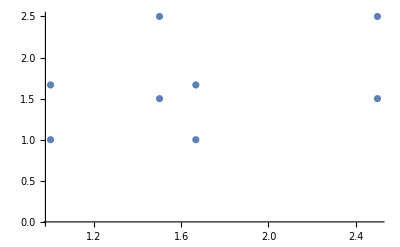

```mathematica
ListPlot[GraphicPointsK1[[1;;8]]]
```

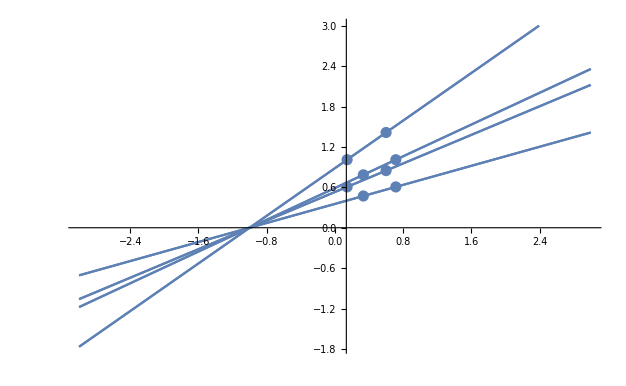

```mathematica
Show[ListPlot[GraphicPointsK2[[1;;8]]],ContourPlot[la.{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lb.{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lc.{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[ld.{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[laPrime.{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lbPrime.{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[lcPrime.{x,y,1}==0,{x,-3,3},{y,-3,3}],ContourPlot[ldPrime.{x,y,1}==0,{x,-3,3},{y,-3,3}],PlotRange->All]
```

```mathematica
NullSpace[F]
```

{{1,0,0}}

```mathematica
LF=Flatten[NullSpace[Transpose[F]]]
```

{-1,0,1}